# Rate equations for ^171Yb ( 1S0 F=1/2→ 3P1 F’ =1/2)

## Author: Hideki Ozawa

```mathematica
ClearAll["Global`*"]
```

## Common part

### Constants

```mathematica
e=1.60217657*10^-19;(*[C]*)
ϵ0=8.85418782*10^-12;(*vacuum permittivity[m^-3 kg^-1 s^4 A^2]*)
c=2.99792458*10^8;(*[m s^-1]*)
hplank=6.62606957*10^-34;(*Plank constant [m^2 kg s^-1]*)
gamma=2π*182*10^3;(*linewidth Γ[rad Hz]*)
a0=5.291772*10^-11;(*Bhor radius[m]*)
```

### Laser field

```mathematica
w0=100*10^-6;(*Beam radius[m]*)
```

### Excited state

```mathematica
fe=1/2; (*Total angular momentum*)
je=1; (*Orbital angular momentum*)
```

### Ground state

```mathematica
f=1/2;
j=0;
nuc=1/2; (*nuclear spin*)
```

### Clebsh-Goldan coefficients

```mathematica
Off[ClebschGordan::phy] (* do not show message even if the answer does not have physical meanings. *)
(*cc[mfe_,mf_]:=((-1)^(fe+je+nuc-mfe+f+1)√((2fe+1)(2f+1)(2je+1))ThreeJSymbol[{fe,-mfe},{1, q},{f,mf}] SixJSymbol[{fe,1,f},{j,nuc,je}])^2;*)
cg[mfe_,mf_]:=((-1)^(fe+je+nuc-mfe+f+1)√((2fe+1)(2f+1)(2je+1))ThreeJSymbol[{fe,-mfe},{1, 0},{f,mf}] SixJSymbol[{fe,1,f},{j,nuc,je}])^2+
((-1)^(fe+je+nuc-mfe+f+1)√((2fe+1)(2f+1)(2je+1))ThreeJSymbol[{fe,-mfe},{1, 1},{f,mf}] SixJSymbol[{fe,1,f},{j,nuc,je}])^2+
((-1)^(fe+je+nuc-mfe+f+1)√((2fe+1)(2f+1)(2je+1))ThreeJSymbol[{fe,-mfe},{1, -1},{f,mf}] SixJSymbol[{fe,1,f},{j,nuc,je}])^2;
```

### Reduced dipole matrix element

```mathematica
dipole=0.54*a0;(*Reduced dipole matrix element [m]*)
```

## Pumping to m_F=-1/2 with initial sate (1/2,1/2)

### Parameters

```mathematica
pow1=20*10^-9;(*[W]Power to pump Subscript[m, F]=+1/2 to Subscript[m, F']=-1/2*)
pow2=0*10^-9;(*[W]Power to pump Subscript[m, F]=+1/2 to Subscript[m, F']=+1/2*)
pow3=20*10^-9;(*[W]Power to pump Subscript[m, F]=-1/2 to Subscript[m, F']=+1/2*)
pow4=0*10^-9;(*[W]Power to pump Subscript[m, F]=-1/2 to Subscript[m, F']=-1/2*)

zeemanShift = 3*10^6; (*[Hz]Zeeman shift of sublevels in F'=1/2*)
lightShift = 0*10^6;(*[Hz]light shift of sublevels in F=1/2*)
detuning1 =2π  0; (*[rad Hz]Detuning of transition between Subscript[m, F]=+1/2, Subscript[m, F']=-1/2 *)
detuning2 =2π  zeemanShift; (*[rad Hz]Detuning of transition between Subscript[m, F]=+1/2, Subscript[m, F']=+1/2 *)
detuning3 =2π  (lightShift+zeemanShift); (*[rad Hz]Detuning of transition between Subscript[m, F]=-1/2, Subscript[m, F']=+1/2 *)
detuning4 =2π  lightShift; (*[rad Hz]Detuning of transition between Subscript[m, F]=-1/2, Subscript[m, F']=-1/2 *)
```

### Calculation part

```mathematica
int1=2 pow1/(π w0^2)(*Peak intensity[W/m^2]*);
int2=2 pow2/(π w0^2)(*Peak intensity[W/m^2]*);
int3=2 pow3/(π w0^2)(*Peak intensity[W/m^2]*);
int4=2 pow4/(π w0^2)(*Peak intensity[W/m^2]*);
```

```mathematica
abs1=(e^2 int1)/(ϵ0 (hplank/(2π))^2 c)1/π(gamma/2)/(detuning1^2+(gamma/2)^2)*cg[-1/2,1/2]/(2 je+1)*dipole^2;(*Stimulated absorption rate [Hz]*)
abs2=(e^2 int2)/(ϵ0 (hplank/(2π))^2 c)1/π(gamma/2)/(detuning2^2+(gamma/2)^2)*cg[1/2,1/2]/(2 je+1)*dipole^2;(*Stimulated absorption rate [Hz]*)
abs3=(e^2 int3)/(ϵ0 (hplank/(2π))^2 c)1/π(gamma/2)/(detuning3^2+(gamma/2)^2)*cg[1/2,-1/2]/(2 je+1)*dipole^2;(*Stimulated absorption rate [Hz]*)
abs4=(e^2 int4)/(ϵ0 (hplank/(2π))^2 c)1/π(gamma/2)/(detuning4^2+(gamma/2)^2)*cg[-1/2,-1/2]/(2 je+1)*dipole^2;(*Stimulated absorption rate [Hz]*)
```

#### Solve 4(2+2) linear-ordinary-differential equations of first order

```mathematica
sol=NDSolve[{n1'[t]==-abs1(n1[t]-nem1[t])-abs2(n1[t]-ne1[t])+gamma (cg[1/2,1/2]ne1[t]+cg[-1/2,1/2]nem1[t]),
nm1'[t]==-abs3(nm1[t]-ne1[t])-abs4(nm1[t]-nem1[t])+gamma (cg[1/2,-1/2]ne1[t]+cg[-1/2,-1/2]nem1[t]),
ne1'[t]==-abs2(ne1[t]-n1[t])-abs3(ne1[t]-nm1[t])-gamma ne1[t],
nem1'[t]==-abs1(nem1[t]-n1[t])-abs4(nem1[t]-nm1[t])-gamma nem1[t],
n1[0]==1/2,nm1[0]==1/2,ne1[0]==0,nem1[0]==0},{n1,nm1,ne1,nem1},{t,0,10^-3},MaxSteps->30000];
```

### Plot spin-relaxation

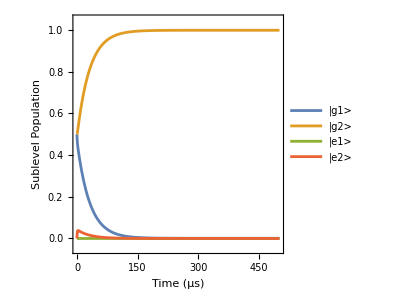

```mathematica
Plot[Evaluate[{n1[t*10^-6],nm1[t*10^-6],ne1[t*10^-6],nem1[t*10^-6]}/.sol],{t,0,500},PlotRange->{-0.05,1.05},AspectRatio->1,ImageSize->300,Frame->True,FrameLabel->{"Time (μs)","Sublevel  Population"},FrameStyle->Directive[16,Black],PlotLegends->LineLegend[Automatic,{"|g1>","|g2>","|e1>","|e2>"}]]
```

```mathematica
Evaluate[nm1[500*10^-6]/.sol]
```

{0.998812}

```mathematica
lightShiftList={0.5,0.75,1,1.25 ,1.5,2,2.5 ,3,4};
poluationAtG2 = {0.9595941128537373,0.98090440225124, 0.98885740508844, 0.992655246112531,0.994763524585,0.9969127983946409,0.9979410235,  0.9985172381883654,0.9991139556};
```

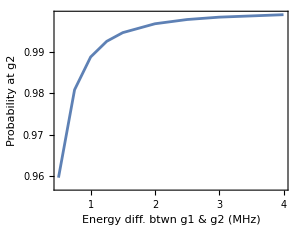

```mathematica
ListPlot[Table[{lightShiftList⟦i⟧,poluationAtG2⟦i⟧},{i,1,Dimensions[lightShiftList]⟦1⟧}],Joined->True,PlotRange->{{0.5,4},All},AspectRatio->0.75,ImageSize->300,Frame->True,FrameLabel->{"Energy diff. btwn g1 & g2 (MHz)","Probability at g2"},FrameStyle->Directive[16,Black]]
```

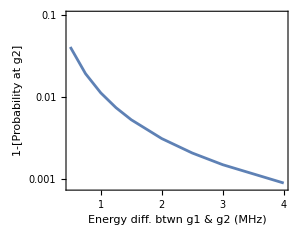

```mathematica
ListLogPlot[Table[{lightShiftList⟦i⟧,1-poluationAtG2⟦i⟧},{i,1,Dimensions[lightShiftList]⟦1⟧}],Joined->True,PlotRange->{{0.5,4},{0.0008,0.1}},AspectRatio->0.75,ImageSize->300,Frame->True,FrameLabel->{"Energy diff. btwn g1 & g2 (MHz)","1-[Probability at g2]"},FrameStyle->Directive[16,Black]]
```